```mathematica
dd[n_, z_, k_] := 1+(z-k+1)/k Sum[ dd[Floor[ n/j], z, k+1 ], {j,2,n}]
```

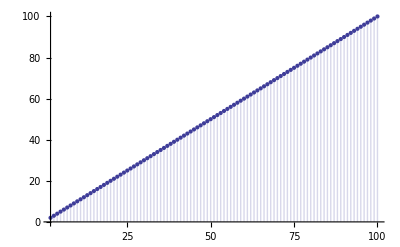

```mathematica
DiscretePlot[ dd[ n, 1, 1],{n,2,100}]
```

```mathematica
num[c_]:=Numerator[c];den[c_]:=Denominator[c]
alpha[n_,c_]:=alpha[n,c]=den[c] (Floor[n/den[c]]-Floor[(n-1)/den[c]])-num[c] (Floor[n/num[c]]-Floor[(n-1)/num[c]])
ld[n_, z_, k_] := (z-k+1)/k Sum[Log[j] + ld[Floor[ n/j], z, k+1 ], {j,2,n}]
ldx[n_, z_, k_, c_] := den[c]^-1 (z-k+1)/k Sum[ If[ alpha[j,c] ==0,0,alpha[j,c]( Log[j/den[c]] + ldx[den[c]n/j, z, k+1, c ])], {j,1+den[c],den[c]n}]
ldxm1[n_, z_, k_, c_] := den[c]^-1 (z-k+1)/k Sum[ If[ alpha[j,c] ==0,0,alpha[j,c]( Log[j/den[c]] + ldxm1[den[c]n/j, z, k+1, c ])], {j,1+den[c],den[c]n-1}]
```

```mathematica
N[ld[100,1,1]]
```

363.739

```mathematica
N[ldx[100,-1,1,3/2]]
```

9.95352

```mathematica
N[L1[ 100, -1, 3/2]]
```

9.95352

```mathematica
FullSimplify[ldx[20,1,1,3/2]-ldxm1[20,1,1,3/2]]
```

Log[20]